```mathematica
tweets = Import["/Users/beto/Documents/08_MY_DATA_ANALYSIS/Airlines_Mathematica/Tweets.csv","CSV"];

tweetid = tweets[[All,1]][[2;;Length[tweets]]];
airlineSentiment= tweets[[All,2]][[2;;Length[tweets]]];
airlineSentimentConfidence = tweets[[All,3]][[2;;Length[tweets]]];
negativereasonArray=tweets[[All,4]][[2;;Length[tweets]]];
negativeReasonConfidence = tweets[[All,5]][[2;;Length[tweets]]];
airline=tweets[[All,6]][[2;;Length[tweets]]];
airlineSentimentGold = tweets[[All,7]][[2;;Length[tweets]]];
name = tweets[[All,8]][[2;;Length[tweets]]];
negativeReasonGold = tweets[[All,9]][[2;;Length[tweets]]];
retweetCount = tweets[[All,10]][[2;;Length[tweets]]];
text = tweets[[All,11]][[2;;Length[tweets]]];
tweetCoord = tweets[[All,12]][[2;;Length[tweets]]];
tweetCreated = tweets[[All,13]][[2;;Length[tweets]]];
tweetLocation = tweets[[All,14]][[2;;Length[tweets]]];
userTimezone = tweets[[All,15]][[2;;Length[tweets]]];

Column[tweets[[1]]]
```

tweet_id
airline_sentiment
airline_sentiment_confidence
negativereason
negativereason_confidence
airline
airline_sentiment_gold
name
negativereason_gold
retweet_count
text
tweet_coord
tweet_created
tweet_location
user_timezone

<|negative→0.626913,neural→0.21168,positive→0.161407|>

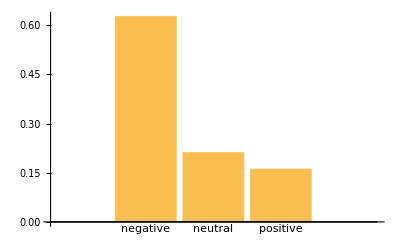

-Graphics-

```mathematica
airlineSentiment= tweets[[All,2]][[2;;Length[tweets]]];
frequencies = {negFreq = N[ Count[airlineSentiment,"negative"]/(Length[tweets]-1)],
neutralFreq = N[ Count[airlineSentiment,"neutral"]/(Length[tweets]-1)],
posFreq = N[ Count[airlineSentiment,"positive"]/(Length[tweets]-1)]};
AssociationThread[{"negative","neural","positive"},frequencies]
BarChart[frequencies,ChartLabels->{"negative","neutral","positive"}]
PieChart[frequencies, ChartLabels->{"negative","neutral","positive"}]
```

<|Virgin America→0.0344262,United→0.261066,Southwest→0.165301,Delta→0.151776,US Airways→0.198975,American→0.188456|>

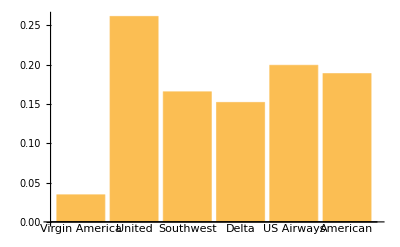

```mathematica
airline=tweets[[All,6]][[2;;Length[tweets]]];
airlineNames = DeleteDuplicates[airline];
percentTweetsByAirline=Table[N[Count[airline,airlineNames[[i]]]/Length[airline]],{i,1,Length[airlineNames],1}];
AssociationThread[airlineNames,percentTweetsByAirline]
BarChart[percentTweetsByAirline,ChartLabels->airlineNames]
```

Virgin America | United | Southwest | Delta | US Airways | American
0.0123634
0.0116803
0.0103825 | 0.17985
0.0476093
0.0336066 | 0.0810109
0.0453552
0.0389344 | 0.0652322
0.0493852
0.0371585 | 0.154577
0.0260246
0.0183743 | 0.13388
0.0316257
0.0229508

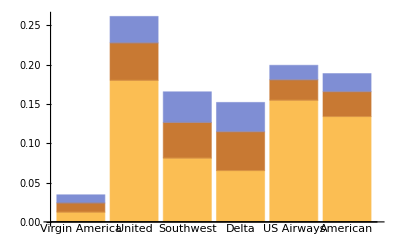

```mathematica
percentagesSentimentByAirline=Table[{N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"negative"]/Length[airline]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"neutral"]/Length[airline]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"positive"]/Length[airline]]},{i,1,Length[airlineNames],1}];
{airlineNames,percentagesSentimentByAirline}//TableForm
BarChart[percentagesSentimentByAirline,ChartLabels-> {Placed[airlineNames, Axis],None}, ChartLayout->"Stacked"]
```

Virgin America | United | Southwest | Delta | US Airways | American
0.359127
0.339286
0.301587 | 0.688906
0.182365
0.128728 | 0.490083
0.27438
0.235537 | 0.429793
0.325383
0.244824 | 0.776862
0.130793
0.0923447 | 0.710402
0.167814
0.121783

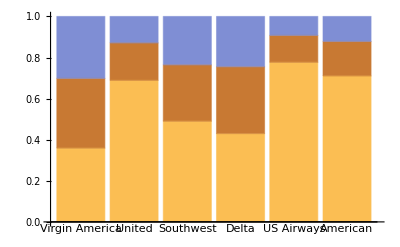

```mathematica
totalCasesByAirline = Table[Count[airline,airlineNames[[j]]],{j,1,Length[airlineNames],1}];
percentagesSentimentByAirline100=Table[{N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"negative"]/totalCasesByAirline[[i]]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"neutral"]/totalCasesByAirline[[i]]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"positive"]/totalCasesByAirline[[i]]]},{i,1,Length[airlineNames],1}];
{airlineNames,percentagesSentimentByAirline100}//TableForm
BarChart[percentagesSentimentByAirline100,ChartLabels-> {Placed[airlineNames, Axis],None}, ChartLayout->"Stacked"]
```

<|→0.373087,Bad Flight→0.0396175,Can't Tell→0.0812842,Late Flight→0.11373,Customer Service Issue→0.19877,Flight Booking Problems→0.0361339,Lost Luggage→0.0494536,Flight Attendant Complaints→0.0328552,Cancelled Flight→0.0578552,Damaged Luggage→0.00505464,longlines→0.0121585|>

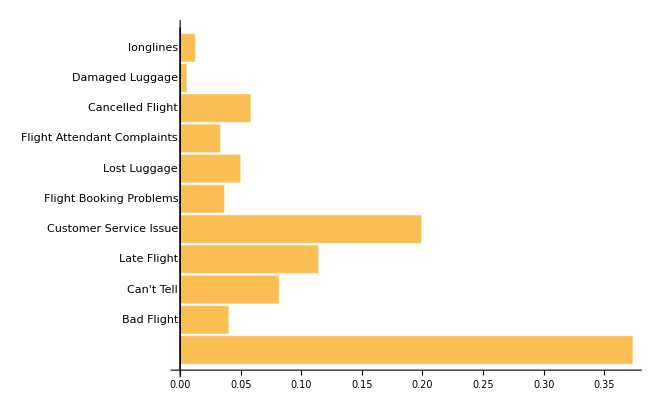

```mathematica
negativereasonArray=tweets[[All,4]][[2;;Length[tweets]]];
cleanNegativereasonArray=tweets[[All,4]][[2;;Length[tweets]]](*/.""->Sequence[]*);
negativereason=DeleteDuplicates[cleanNegativereasonArray];
FreqNegativeReasons=Table[N[Count[cleanNegativereasonArray,negativereason[[i]]]/Length[negativereasonArray]],{i,1,Length[negativereason],1}];
AssociationThread[negativereason,FreqNegativeReasons]
BarChart[FreqNegativeReasons,BarOrigin->Left,ChartLabels->negativereason]
```

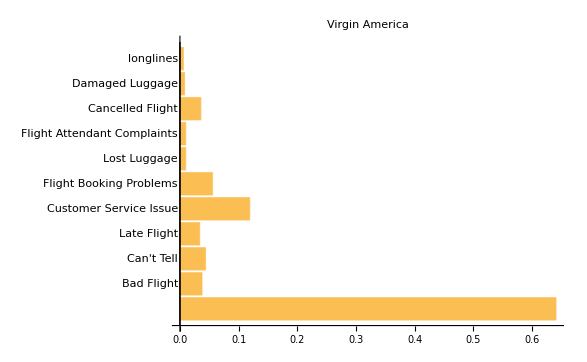
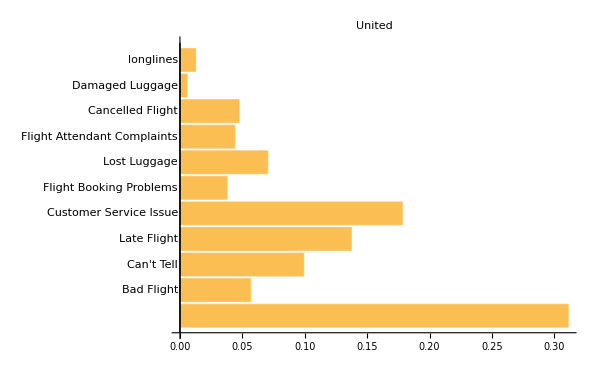
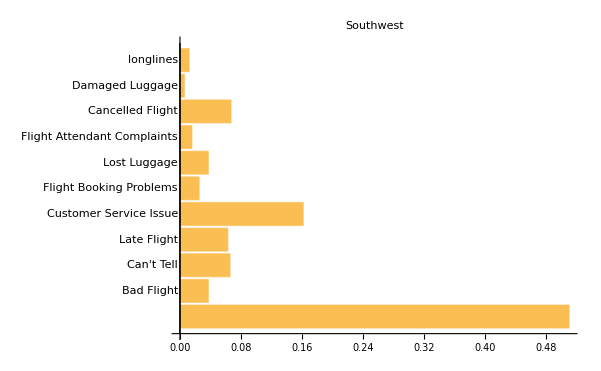
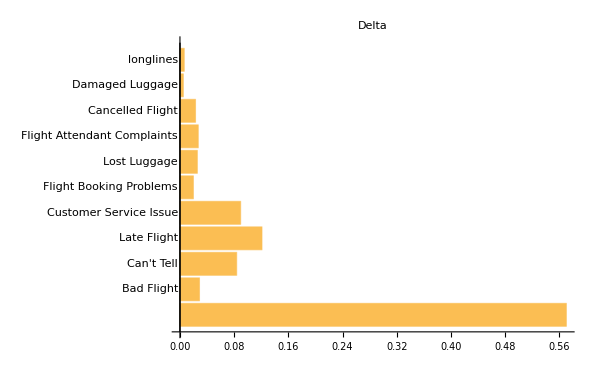
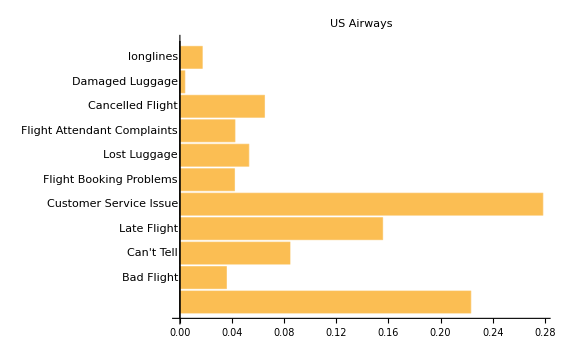
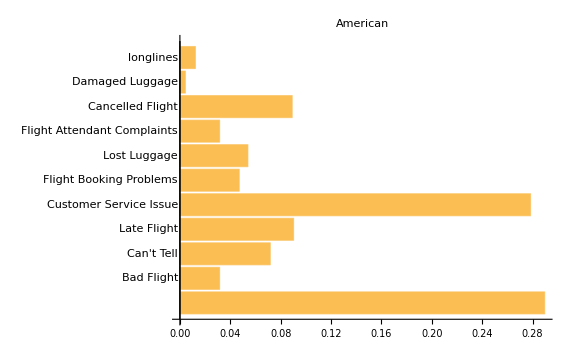

```mathematica
Table[
negReasonsByAirline = Extract[negativereasonArray,Position[airline,airlineNames[[j]]]](*/.""->Sequence[]*);
BarChart[Table[Count[negReasonsByAirline,negativereason[[i]]],{i,1,Length[negativereason],1}]/Length[negReasonsByAirline],BarOrigin->Left,ChartLabels->negativereason,PlotLabel->airlineNames[[j]]],{j,1,Length[airlineNames],1}]
```

```mathematica
{Column[tweets[[1]]],Column[{
NANtweetid = Length[tweetid]-Length[tweetid/.""-> Sequence[]],
NANairlineSentiment= Length[airlineSentiment]-Length[airlineSentiment/.""-> Sequence[]],
NANairlineSentimentConfidence = Length[airlineSentimentConfidence]-Length[airlineSentimentConfidence/.""-> Sequence[]],
NANnegativereasonArray=Length[negativereasonArray]-Length[negativereasonArray/.""-> Sequence[]],
NANnegativeReasonConfidence = Length[negativeReasonConfidence]-Length[negativeReasonConfidence/.""-> Sequence[]],
NANairline=Length[airline]-Length[airline/.""-> Sequence[]],
NANairlineSentimentGold =Length[airlineSentimentGold ]-Length[airlineSentimentGold /.""-> Sequence[]],
NANname = Length[name]-Length[name/.""-> Sequence[]],
NANnegativeReasonGold = Length[negativeReasonGold]-Length[negativeReasonGold/.""-> Sequence[]],
NANretweetCount = Length[retweetCount ]-Length[retweetCount /.""-> Sequence[]],
NANtext = Length[text ]-Length[text /.""-> Sequence[]],
NANtweetCoord = Length[tweetCoord]-Length[tweetCoord/.""-> Sequence[]],
NANtweetCreated =Length[tweetCreated ]-Length[tweetCreated /.""-> Sequence[]],
NANtweetLocation = Length[tweetLocation]-Length[tweetLocation/.""-> Sequence[]],
NANuserTimezone = Length[userTimezone]-Length[userTimezone/.""-> Sequence[]]}]}
```

{tweet_id
airline_sentiment
airline_sentiment_confidence
negativereason
negativereason_confidence
airline
airline_sentiment_gold
name
negativereason_gold
retweet_count
text
tweet_coord
tweet_created
tweet_location
user_timezone,0
0
0
5462
4118
0
14600
0
14608
0
0
13621
0
4733
4820}

```mathematica
timesRetweeted =Sort[DeleteDuplicates[retweetCount]];
freqRetweeted=Table[Count[retweetCount,Part[timesRetweeted,i]],{i,1,Length[timesRetweeted],1}];
Print["timesRetweeted   frequency"];
{Column[timesRetweeted],Column[freqRetweeted]}//TableView
```

timesRetweeted   frequency

TableView[{0
1
2
3
4
5
6
7
8
9
11
15
18
22
28
31
32
44,13873
640
66
22
17
5
3
3
1
1
1
1
1
2
1
1
1
1}]

```mathematica
text[[Flatten[Position[retweetCount,44]]]]
text[[Flatten[Position[retweetCount,32]]]]
text[[Flatten[Position[retweetCount,31]]]]
text[[Flatten[Position[retweetCount,28]]]]
```

{@USAirways 5 hr flight delay and a delay when we land . Is that even real life ? Get me off this plane , I wanna go home ð.9f.91 ð.9f.91 ð.9f.91  (3 heel clicks)}

{@USAirways of course never again tho . Thanks for tweetin ur concern but not Doin anythin to fix what happened. I'll choose wiser next time}

{STOP. USING.THIS.WORD. IF. YOU'RE. A. COMPANY. RT @JetBlue: Our fleet's on fleek. http://t.co/Fd2TNYcTrB}

{@USAirways with this livery back in the day. http://t.co/EEqWVAMmiy}

```mathematica
DeleteDuplicates[tweetLocation][[2;;50]]
```

{Lets Play,San Francisco CA,Los Angeles,San Diego,1/1 loner squad,NYC,San Francisco, CA,palo alto, ca,west covina,this place called NYC,Somewhere celebrating life.,Boston | Waltham,Boston, MA ,714,San Mateo, CA & Las Vegas, NV,Brooklyn,California, San Francisco,Washington DC,Texas,Worldwide,Central Texas,i'm creating a monster,Iowa City,Georgia,Turks and caicos,Oakland via Midwest,New York, NY,Northern Virginia,Los Angeles / Atlanta,new york, new york,brooklyn, Ny,Bali, Republic of Indonesia,UK, USA. ,Gold Coast, Australia,Stockton, CA,Twin Cities, Minn.,USA,next city,SF â.86.94 NY,New York + Panama,London, England,Floridian from Cincinnati,Dallas, Texas,Seattle, WA,Lower Pacific Heights, SF, CA,Chicago,Los Cabos,Mexico,Los Angeles, CA,Austin, TX}

```mathematica
tzones=DeleteDuplicates[userTimezone];
cleanUserTimezone = Flatten[{userTimezone}/.""->Sequence[]];
freqTZones=Table[N[Count[cleanUserTimezone,tzones[[i]]]/Length[cleanUserTimezone]],{i,1,Length[tzones],1}];
Reverse[Sort[AssociationThread[tzones,freqTZones]]][[1;;10]]
```

<|Eastern Time (US & Canada)→0.381263,Central Time (US & Canada)→0.19664,Pacific Time (US & Canada)→0.123014,Quito→0.0751527,Atlantic Time (Canada)→0.050611,Mountain Time (US & Canada)→0.0375764,Arizona→0.0233198,London→0.0198574,Alaska→0.010998,Sydney→0.0108961|>

```mathematica
coordinatesInNumber=Flatten@ToExpression@StringSplit[StringReplace[#,{"["-> "","]"-> ""}],","]&/@tweetCoord(*/.{}->Sequence[]*);
coordinates = DeleteDuplicates[coordinatesInNumber];
coordinates = coordinates[[2;;Length[coordinates]]]/.{0.,0.}-> Sequence[];
freqTweetCoord = Table[Count[coordinatesInNumber,coordinates[[i]]],{i,1,Length[coordinates],1}];
data=Table[GeoPosition[coordinates[[i]]]->freqTweetCoord[[i]],{i,1,Length[coordinates]}];
GeoBubbleChart[data, GeoRange->"World"]
```

-Graphics-

```mathematica
data=Table[GeoPosition[{RandomReal[{-60,60}],RandomReal[{-120,0}]}]->RandomReal[10],2,5]
GeoBubbleChart[data]
```

{{GeoPosition[{-56.7624,-30.0612}]→8.72073,GeoPosition[{-21.9728,-94.7838}]→7.01881,GeoPosition[{29.7147,-72.185}]→5.13739,GeoPosition[{33.9791,-98.1063}]→0.988314,GeoPosition[{-12.7506,-48.5418}]→5.63689},{GeoPosition[{23.2225,-39.9183}]→3.02444,GeoPosition[{-40.4071,-32.02}]→5.18784,GeoPosition[{-6.69914,-83.2515}]→6.76319,GeoPosition[{51.3865,-59.8623}]→0.525307,GeoPosition[{-51.4575,-28.9618}]→0.0404816}}

-Graphics-

```mathematica
GeoListPlot[{Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"LosAngeles","California","UnitedStates"}]}]
GeoBubbleChart[data, GeoRange -> LinguisticAssistant]








computeAll[]:=Module[
{airlineSentiment,frequencies,negFreq,neutralFreq,posFreq,table1}
,
airlineSentiment= tweets[[All,2]][[2;;Length[tweets]]];
Print[Style["Data description",FontSize-> 30]];
headers=Column[tweets[[1]]];
Print[headers];
frequencies = {negFreq = N[ Count[airlineSentiment,"negative"]/(Length[tweets]-1)],
neutralFreq = N[ Count[airlineSentiment,"neutral"]/(Length[tweets]-1)],
posFreq = N[ Count[airlineSentiment,"positive"]/(Length[tweets]-1)]};

table1=AssociationThread[{"negative","neural","positive"},frequencies];
Print[Style["Proportion of tweets with each sentiment",FontSize-> 30]];
Print[table1];
bc1=BarChart[frequencies,ChartLabels->{"negative","neutral","positive"}];
bc2=PieChart[frequencies, ChartLabels->{"negative","neutral","positive"}];
Print[bc1];
Print[bc2];

airline=tweets[[All,6]][[2;;Length[tweets]]];
airlineNames = DeleteDuplicates[airline];
percentTweetsByAirline=Table[N[Count[airline,airlineNames[[i]]]/Length[airline]],{i,1,Length[airlineNames],1}];

Print[Style["Proportion of tweets per airline",FontSize-> 30]];
table2=AssociationThread[airlineNames,percentTweetsByAirline];
Print[table2];
bc3=BarChart[percentTweetsByAirline,ChartLabels->airlineNames];
Print[bc3];

percentagesSentimentByAirline=Table[{N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"negative"]/Length[airline]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"neutral"]/Length[airline]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"positive"]/Length[airline]]},{i,1,Length[airlineNames],1}];

table3={airlineNames,percentagesSentimentByAirline}//TableForm;
Print[Style["Proportion of sentiment tweets per airline (negative, neutral, positive)",FontSize-> 30]];
Print[table3];
bc4=BarChart[percentagesSentimentByAirline,ChartLabels-> {Placed[airlineNames, Axis],None}, ChartLayout->"Stacked"];
Print[bc4];


totalCasesByAirline = Table[Count[airline,airlineNames[[j]]],{j,1,Length[airlineNames],1}];
percentagesSentimentByAirline100=Table[{N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"negative"]/totalCasesByAirline[[i]]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"neutral"]/totalCasesByAirline[[i]]],N[Count[Extract[airlineSentiment,Position[airline,airlineNames[[i]]]],"positive"]/totalCasesByAirline[[i]]]},{i,1,Length[airlineNames],1}];

table4={airlineNames,percentagesSentimentByAirline100}//TableForm;
bc5=BarChart[percentagesSentimentByAirline100,ChartLabels-> {Placed[airlineNames, Axis],None}, ChartLayout->"Stacked"];
Print[table4];
Print[bc5];


negativereasonArray=tweets[[All,4]][[2;;Length[tweets]]];
cleanNegativereasonArray=tweets[[All,4]][[2;;Length[tweets]]](*/.""->Sequence[]*);
negativereason=DeleteDuplicates[cleanNegativereasonArray];
FreqNegativeReasons=Table[N[Count[cleanNegativereasonArray,negativereason[[i]]]/Length[negativereasonArray]],{i,1,Length[negativereason],1}];

table5=AssociationThread[negativereason,FreqNegativeReasons];
Print[Style["Reasons for negative sentiment tweets",FontSize-> 30]];
bc6=BarChart[FreqNegativeReasons,BarOrigin->Left,ChartLabels->negativereason];
Print[{Column[Keys[table5]],Column[Values[table5]]}];
Print[bc6];

Print[Style["Reasons for negative sentiment per airline",FontSize-> 30]];
For[ j=1,j≤ Length[airlineNames],j++,
negReasonsByAirline = Extract[negativereasonArray,Position[airline,airlineNames[[j]]]](*/.""->Sequence[]*);
bcx=BarChart[Table[Count[negReasonsByAirline,negativereason[[i]]],{i,1,Length[negativereason],1}]/Length[negReasonsByAirline],BarOrigin->Left,ChartLabels->negativereason,PlotLabel->airlineNames[[j]]];
Print[bcx];
];

<|"BC1"->GraphicsGrid[Image[bc1],Image[bc2]]|>


];
```

-Graphics-

-Graphics-

Data description

tweet_id
airline_sentiment
airline_sentiment_confidence
negativereason
negativereason_confidence
airline
airline_sentiment_gold
name
negativereason_gold
retweet_count
text
tweet_coord
tweet_created
tweet_location
user_timezone

Proportion of tweets with each sentiment

<|negative→0.626913,neural→0.21168,positive→0.161407|>

-Graphics-

-Graphics-

Proportion of tweets per airline

<|Virgin America→0.0344262,United→0.261066,Southwest→0.165301,Delta→0.151776,US Airways→0.198975,American→0.188456|>

-Graphics-

Proportion of sentiment tweets per airline (negative, neutral, positive)

Virgin America | United | Southwest | Delta | US Airways | American
0.0123634
0.0116803
0.0103825 | 0.17985
0.0476093
0.0336066 | 0.0810109
0.0453552
0.0389344 | 0.0652322
0.0493852
0.0371585 | 0.154577
0.0260246
0.0183743 | 0.13388
0.0316257
0.0229508

-Graphics-

Virgin America | United | Southwest | Delta | US Airways | American
0.359127
0.339286
0.301587 | 0.688906
0.182365
0.128728 | 0.490083
0.27438
0.235537 | 0.429793
0.325383
0.244824 | 0.776862
0.130793
0.0923447 | 0.710402
0.167814
0.121783

-Graphics-

Reasons for negative sentiment tweets

{
Bad Flight
Can't Tell
Late Flight
Customer Service Issue
Flight Booking Problems
Lost Luggage
Flight Attendant Complaints
Cancelled Flight
Damaged Luggage
longlines,0.373087
0.0396175
0.0812842
0.11373
0.19877
0.0361339
0.0494536
0.0328552
0.0578552
0.00505464
0.0121585}

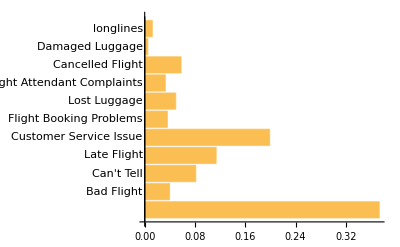

Reasons for negative sentiment per airline

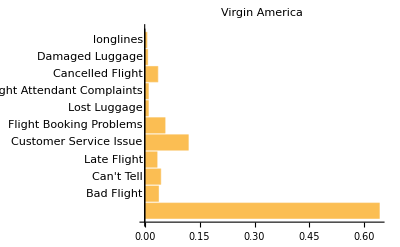

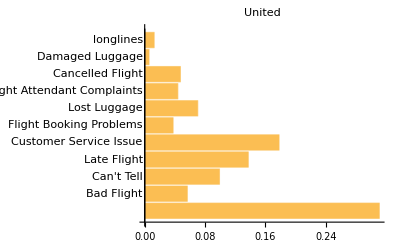

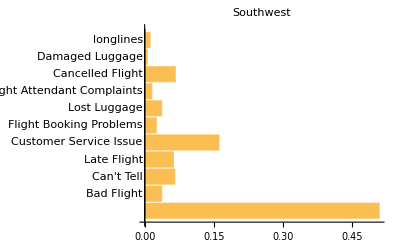

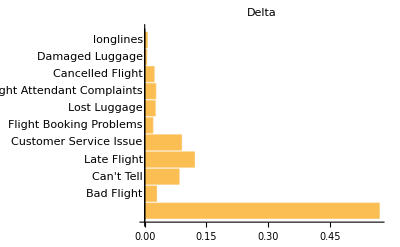

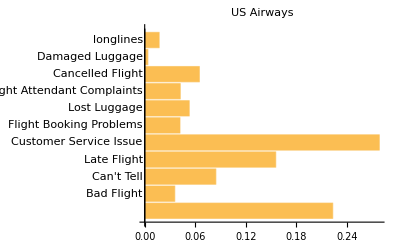

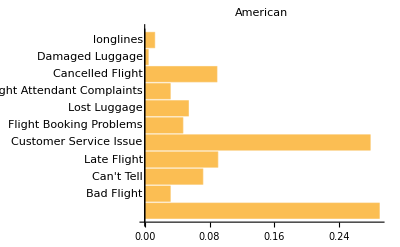

<|BC1→-Graphics-|>

```mathematica
computeAll[]
```

```mathematica
simpleFunc[]:=computeAll[];
CloudDeploy[FormFunction[{},simpleFunc[]],Permissions->"Public"]
```

Data description

tweet_id
airline_sentiment
airline_sentiment_confidence
negativereason
negativereason_confidence
airline
airline_sentiment_gold
name
negativereason_gold
retweet_count
text
tweet_coord
tweet_created
tweet_location
user_timezone

Proportion of tweets with each sentiment

<|negative→0.626913,neural→0.21168,positive→0.161407|>

-Graphics-

-Graphics-

Proportion of tweets per airline

<|Virgin America→0.0344262,United→0.261066,Southwest→0.165301,Delta→0.151776,US Airways→0.198975,American→0.188456|>

-Graphics-

Proportion of sentiment tweets per airline (negative, neutral, positive)

Virgin America | United | Southwest | Delta | US Airways | American
0.0123634
0.0116803
0.0103825 | 0.17985
0.0476093
0.0336066 | 0.0810109
0.0453552
0.0389344 | 0.0652322
0.0493852
0.0371585 | 0.154577
0.0260246
0.0183743 | 0.13388
0.0316257
0.0229508

-Graphics-

Virgin America | United | Southwest | Delta | US Airways | American
0.359127
0.339286
0.301587 | 0.688906
0.182365
0.128728 | 0.490083
0.27438
0.235537 | 0.429793
0.325383
0.244824 | 0.776862
0.130793
0.0923447 | 0.710402
0.167814
0.121783

-Graphics-

Reasons for negative sentiment tweets

{
Bad Flight
Can't Tell
Late Flight
Customer Service Issue
Flight Booking Problems
Lost Luggage
Flight Attendant Complaints
Cancelled Flight
Damaged Luggage
longlines,0.373087
0.0396175
0.0812842
0.11373
0.19877
0.0361339
0.0494536
0.0328552
0.0578552
0.00505464
0.0121585}

-Graphics-

Reasons for negative sentiment per airline

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

GraphicsGrid::list: … is not a list of lists.

CloudObject[https://www.wolframcloud.com/objects/17def740-1750-48a3-93d9-4ac3bb83bf2a]